## Check of F000:

F000 = ∫_x^∞ ⅇ^(2ⅈ u)/u(∫_u^∞ ⅇ^(-2ⅈ t)/t(∫_t^∞ ⅇ^(2ⅈ s)/s ⅆs)ⅆt)ⅆu)= ∫_x^∞ ⅇ^(2ⅈ u)/u F00 du.

We computed for F00 its exact solution and its super-Hubble limit.

```mathematica
F00= 1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ x]+32 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]+8 (-2+α) Log[x]-4 Log[x] (-2 CosIntegral[2 x]+Log[x]+2 ⅈ SinIntegral[2 x])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ x]); 
F00lim = (B^2/2+π^2/4+4 ⅈ u-2 ⅈ B u+B Log[u]-2 ⅈ u Log[u]+Log[u]^2/2)
```

```mathematica
FullSimplify[Integrate[ⅇ^(2ⅈ u)/u(1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ u])),{u, x,1}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

∫_x^1 1/(8 u)ⅇ^(2 ⅈ u) (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Hypergeometric1F1^(2,0,0)[0,1,-2 ⅈ u])ⅆu

Mathematica is not able to perform the integration, neither if we set the upper bound of the integral as 1 instead of +∞. Then, we choose to keep the limit form of F00 up to O(u^0):

```mathematica
FullSimplify[Integrate[ⅇ^(2ⅈ u)/u(B^2/2+π^2/4+B Log[u]+Log[u]^2/2),{u, x,+∞}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

(B EulerGamma^2)/2-EulerGamma^3/6+1/4 ⅈ B^2 π-1/2 ⅈ B EulerGamma π+1/4 ⅈ EulerGamma^2 π-(B π^2)/24+(EulerGamma π^2)/24+(7 ⅈ π^3)/48-1/2 B^2 CosIntegral[2 x]-1/4 π^2 CosIntegral[2 x]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]-1/2 EulerGamma^2 Log[2]-1/2 ⅈ B π Log[2]+1/2 ⅈ EulerGamma π Log[2]-Log[2]^3/6+1/48 π^2 Log[4]+1/6 B Log[2] Log[8]-1/6 EulerGamma Log[2] Log[8]+1/12 ⅈ π Log[2] Log[8]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+1/4 B Log[16] Log[x]+1/2 B Log[x]^2+1/2 EulerGamma Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+1/12 Log[64] Log[x]^2+Log[x]^3/3+B EulerGamma Log[2 x]-1/2 ⅈ B^2 SinIntegral[2 x]-1/4 ⅈ π^2 SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x]-Zeta[3]/3

```mathematica
FullSimplify[Normal[Series[(B EulerGamma^2)/2-EulerGamma^3/6+1/4 ⅈ B^2 π-1/2 ⅈ B EulerGamma π+1/4 ⅈ EulerGamma^2 π-(B π^2)/24+(EulerGamma π^2)/24+(7 ⅈ π^3)/48-1/2 B^2 CosIntegral[2 x]-1/4 π^2 CosIntegral[2 x]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]-1/2 EulerGamma^2 Log[2]-1/2 ⅈ B π Log[2]+1/2 ⅈ EulerGamma π Log[2]-Log[2]^3/6+1/48 π^2 Log[4]+1/6 B Log[2] Log[8]-1/6 EulerGamma Log[2] Log[8]+1/12 ⅈ π Log[2] Log[8]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+1/4 B Log[16] Log[x]+1/2 B Log[x]^2+1/2 EulerGamma Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+1/12 Log[64] Log[x]^2+Log[x]^3/3+B EulerGamma Log[2 x]-1/2 ⅈ B^2 SinIntegral[2 x]-1/4 ⅈ π^2 SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x]-Zeta[3]/3,{x,0,1}]]  /.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

-B^3/6-(B π^2)/4-2 ⅈ x+2 ⅈ B x-ⅈ B^2 x-1/2 ⅈ π^2 x-1/2 B^2 Log[x]-1/4 π^2 Log[x]+2 ⅈ x Log[x]-2 ⅈ B x Log[x]-1/2 B Log[x]^2-ⅈ x Log[x]^2-Log[x]^3/6-Zeta[3]/3

We now plot F00 to understand if our approximation was worth or not.

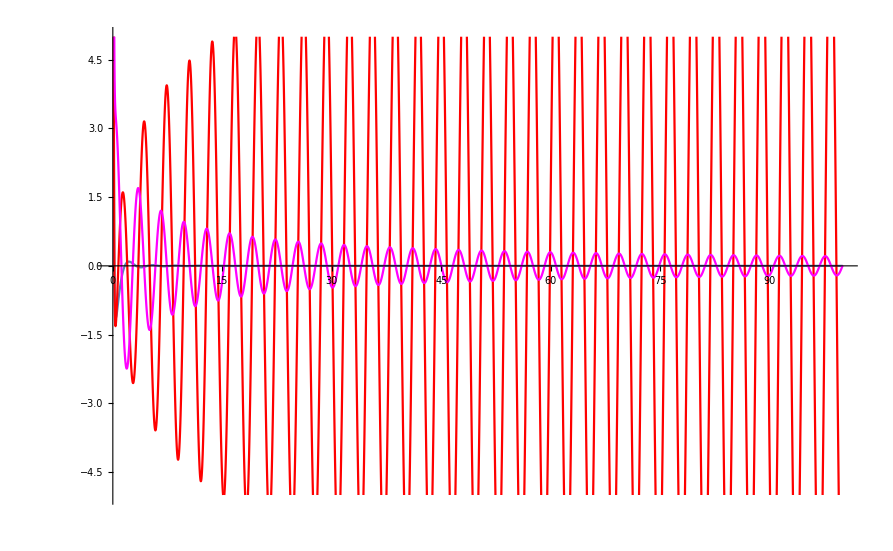

```mathematica
α =-EulerGamma+2-Log[2];
B = EulerGamma+Log[2]-(ⅈ π)/2;
Int1[x_] :=Re[ⅇ^(2ⅈ x)/x 1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ x]+32 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]+8 (-2+α) Log[x]-4 Log[x] (-2 CosIntegral[2 x]+Log[x]+2 ⅈ SinIntegral[2 x])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ x])];
Int2[x_]:=Re[ⅇ^(2ⅈ x)/x( (B^2/2+π^2/4+4 ⅈ x-2 ⅈ B x+B Log[x]-2 ⅈ x Log[x]+Log[x]^2/2))];
Int3[x_]:=Re[ⅇ^(2ⅈ x)/x( (B^2/2+π^2/4+B Log[x]+Log[x]^2/2))];
p1 = Plot[Int1[x],{x,0.0001,100}, PlotRange->{-5,5}];
p2 = Plot[Int2[x],{x,0.0001,100}, PlotStyle->Red, PlotRange->{-5,5}];
p3 =  Plot[Int3[x],{x,0.0001,100}, PlotStyle->Magenta, PlotRange->{-5,5}];
Show[p1,p2,p3]
```

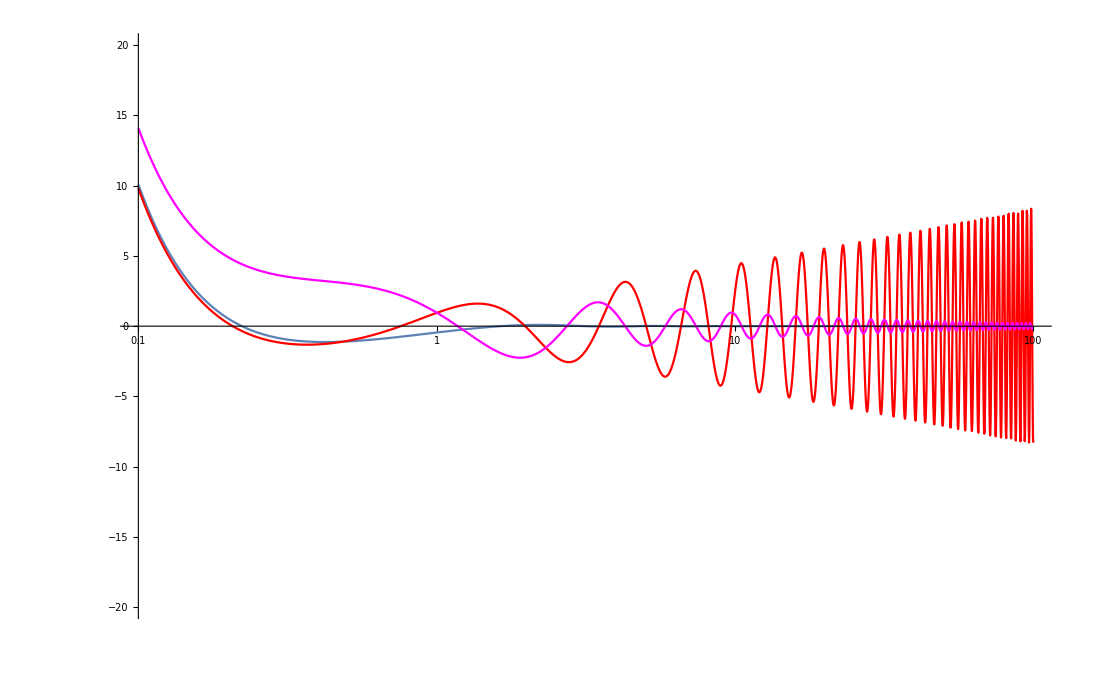

```mathematica
p11 = LogLinearPlot[Int1[x],{x,0.1,100}, PlotRange->{-20,20}];
p22 =LogLinearPlot[Int2[x],{x,0.1,100}, PlotStyle->Red, PlotRange->{-20,20}];
p33 =  LogLinearPlot[Int3[x],{x,0.1,100}, PlotStyle->Magenta, PlotRange->{-20,20}];
Show[p11,p22,p33]
```

## How Mathematica is silly and it’s not able to integrate with α

We notice MAthematica is not able to compute the integral if we work with α :

```mathematica
FullSimplify[Normal[Series[(1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ u])),{u,0,0}]]/.EulerGamma->2-α-Log[2]   ,Assumptions->u>0]//Expand
```

2-ⅈ π+π^2/8-2 α+(ⅈ π α)/2+α^2/2+2 Log[u]-1/2 ⅈ π Log[u]-α Log[u]+Log[u]^2/2-1/2 Hypergeometric1F1^(2,0,0)[0,1,0]

The hypergeometric shit is 0:

```mathematica
N[-1/2 Derivative[2,0,0][Hypergeometric1F1][0,1,0]]
```

0.

Now we integrate.

```mathematica
FullSimplify[Integrate[ⅇ^(2ⅈ u)/u(2-ⅈ π+π^2/8-2 α+(ⅈ π α)/2+α^2/2+2 Log[u]-1/2 ⅈ π Log[u]-α Log[u]+Log[u]^2/2),{u, x,+∞}], Assumptions-> u>0, Assumptions-> u>0]//Expand
```

∫_x^∞ (ⅇ^(2 ⅈ u) (π^2+4 ⅈ π (-2+α)+4 (-2+α)^2+4 Log[u] (4-ⅈ π-2 α+Log[u])))/(8 u)ⅆu

This is the same identical integral as the one compute at the beginning but with B. Mathematica seems to have some problems with α.

## Integration with expansion at order u

Let’s expand up to the first order:

```mathematica
FullSimplify[Normal[Series[(1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ u])),{u,0,1}]]/. α-> -B-(ⅈ π)/2+2 ,Assumptions->u>0]//Expand
```

Series::ztest1: Unable to decide whether numeric quantity -4 Hypergeometric1F1^(2,0,0)[0,1,0] is equal to zero. Assuming it is.

-B^2/2+B EulerGamma-(ⅈ B π)/2+π^2/4+4 ⅈ u-2 ⅈ B u+1/4 B Log[16]+EulerGamma Log[u]-1/2 ⅈ π Log[u]-2 ⅈ u Log[u]+1/4 Log[16] Log[u]+Log[u]^2/2-1/2 Hypergeometric1F1^(2,0,0)[0,1,0]+ⅈ u Hypergeometric1F1^(2,0,1)[0,1,0]

```mathematica
N[-1/2 Derivative[2,0,0][Hypergeometric1F1][0,1,0]+ⅈ u Derivative[2,0,1][Hypergeometric1F1][0,1,0]]
```

0.+0. ⅈ

```mathematica
FullSimplify[(-B^2/2+B EulerGamma-(ⅈ B π)/2+π^2/4+4 ⅈ u-2 ⅈ B u+1/4 B Log[16]+EulerGamma Log[u]-1/2 ⅈ π Log[u]-2 ⅈ u Log[u]+1/4 Log[16] Log[u]+Log[u]^2/2)/.  EulerGamma-> B-Log[2]+(ⅈ π)/2 ]//Expand
```

B^2/2+π^2/4+4 ⅈ u-2 ⅈ B u+B Log[u]-2 ⅈ u Log[u]+Log[u]^2/2

Now we want to integrate between x and 1 and then compute the error wrt the integration performed from 0 to ∞ using the expression at O(u^0)

```mathematica
FullSimplify[Integrate[ⅇ^(2ⅈ u)/u(B^2/2+π^2/4+4 ⅈ u-2 ⅈ B u+B Log[u]-2 ⅈ u Log[u]+Log[u]^2/2),{u, x,+1}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

ConditionalExpression[2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-2 ⅇ^(2 ⅈ x)+B ⅇ^(2 ⅈ x)+CosIntegral[2]-CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+2 B Log[x]+ⅇ^(2 ⅈ x) Log[x]-B α Log[x]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+Log[x]^2+1/2 B Log[x]^2-1/2 α Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+Log[x]^3/3+ⅈ SinIntegral[2]-ⅈ SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x],x<1]

```mathematica
FullSimplify[(2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-2 ⅇ^(2 ⅈ x)+B ⅇ^(2 ⅈ x)+CosIntegral[2]-CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+2 B Log[x]+ⅇ^(2 ⅈ x) Log[x]-B α Log[x]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+Log[x]^2+1/2 B Log[x]^2-1/2 α Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+Log[x]^3/3+ⅈ SinIntegral[2]-ⅈ SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x])/. α-> -B-(ⅈ π)/2+2]//Expand
```

2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-2 ⅇ^(2 ⅈ x)+B ⅇ^(2 ⅈ x)+CosIntegral[2]-CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+B^2 Log[x]+ⅇ^(2 ⅈ x) Log[x]+1/2 ⅈ B π Log[x]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+B Log[x]^2+1/4 ⅈ π Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+Log[x]^3/3+ⅈ SinIntegral[2]-ⅈ SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x]

```mathematica
FullSimplify[Normal[Series[2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-2 ⅇ^(2 ⅈ x)+B ⅇ^(2 ⅈ x)+CosIntegral[2]-CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+B^2 Log[x]+ⅇ^(2 ⅈ x) Log[x]+1/2 ⅈ B π Log[x]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+B Log[x]^2+1/4 ⅈ π Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+Log[x]^3/3+ⅈ SinIntegral[2]-ⅈ SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x],{x,0,0}]]  /.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

-2-B^3/2+2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-ⅈ π-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6

Let’s compare it with the above solution

```mathematica
FullSimplify[(-2-B^3/2+2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-ⅈ π-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6)-(-B^3/6-(B π^2)/4-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6-Zeta[3]/3)]//Expand
```

-2-B^3/3+2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-ⅈ π-1/2 ⅈ B^2 π-(ⅈ π^3)/4+ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]+Zeta[3]/3

Let’s evaluate this difference

```mathematica
B = EulerGamma+Log[2]-(ⅈ π)/2
N[-2-B^3/3+2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-ⅈ π-1/2 ⅈ B^2 π-(ⅈ π^3)/4+ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]+Zeta[3]/3]
```

EulerGamma-(ⅈ π)/2+Log[2]

-2.10453-0.622397 ⅈ

## Integration with expansion at order u^2

Let’s expand up to the first order:

```mathematica
FullSimplify[Normal[Series[(1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ u])),{u,0,2}]]/. α-> -B-(ⅈ π)/2+2 ,Assumptions->u>0]//Expand
```

Series::ztest1: Unable to decide whether numeric quantity -4 Hypergeometric1F1^(2,0,0)[0,1,0] is equal to zero. Assuming it is.

-B^2/2+B EulerGamma-(ⅈ B π)/2+π^2/4+4 ⅈ u-2 ⅈ B u+u^2-B u^2+1/4 B Log[16]+EulerGamma Log[u]-1/2 ⅈ π Log[u]-2 ⅈ u Log[u]-u^2 Log[u]+1/4 Log[16] Log[u]+Log[u]^2/2-1/2 Hypergeometric1F1^(2,0,0)[0,1,0]+ⅈ u Hypergeometric1F1^(2,0,1)[0,1,0]+u^2 Hypergeometric1F1^(2,0,2)[0,1,0]

```mathematica
N[-1/2 Derivative[2,0,0][Hypergeometric1F1][0,1,0]+ⅈ u Derivative[2,0,1][Hypergeometric1F1][0,1,0]+u^2 Derivative[2,0,2][Hypergeometric1F1][0,1,0]]
```

(0.+0. ⅈ)+1. u^2

```mathematica
FullSimplify[(-B^2/2+B EulerGamma-(ⅈ B π)/2+π^2/4+4 ⅈ u-2 ⅈ B u+u^2-B u^2+1/4 B Log[16]+EulerGamma Log[u]-1/2 ⅈ π Log[u]-2 ⅈ u Log[u]-u^2 Log[u]+1/4 Log[16] Log[u]+Log[u]^2/2+u^2)/.  EulerGamma-> B-Log[2]+(ⅈ π)/2 ]//Expand
```

B^2/2+π^2/4+4 ⅈ u-2 ⅈ B u+2 u^2-B u^2+B Log[u]-2 ⅈ u Log[u]-u^2 Log[u]+Log[u]^2/2

Now we want to integrate between x and 1 and then compute the error wrt the integration performed from 0 to ∞ using the expression at O(u^0)

```mathematica
FullSimplify[Integrate[ⅇ^(2ⅈ u)/u(B^2/2+π^2/4+4 ⅈ u-2 ⅈ B u+2 u^2-B u^2+B Log[u]-2 ⅈ u Log[u]-u^2 Log[u]+Log[u]^2/2),{u, x,+1}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

ConditionalExpression[(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-9/4 ⅇ^(2 ⅈ x)+5/4 B ⅇ^(2 ⅈ x)+ⅈ ⅇ^(2 ⅈ x) x-1/2 ⅈ B ⅇ^(2 ⅈ x) x+(5 CosIntegral[2])/4-5/4 CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+2 B Log[x]+5/4 ⅇ^(2 ⅈ x) Log[x]-1/2 ⅈ B π Log[x]-1/2 ⅈ ⅇ^(2 ⅈ x) x Log[x]-B α Log[x]+B ExpIntegralE[1,-2 ⅈ x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+Log[x]^2+1/2 B Log[x]^2-1/4 ⅈ π Log[x]^2-1/2 α Log[x]^2+1/2 ExpIntegralE[1,-2 ⅈ x] Log[x]^2+Log[x]^3/3+5/4 ⅈ SinIntegral[2]-5/4 ⅈ SinIntegral[2 x],x<1]

```mathematica
((9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-9/4 ⅇ^(2 ⅈ x)+5/4 B ⅇ^(2 ⅈ x)+ⅈ ⅇ^(2 ⅈ x) x-1/2 ⅈ B ⅇ^(2 ⅈ x) x+(5 CosIntegral[2])/4-5/4 CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+2 B Log[x]+5/4 ⅇ^(2 ⅈ x) Log[x]-1/2 ⅈ B π Log[x]-1/2 ⅈ ⅇ^(2 ⅈ x) x Log[x]-B α Log[x]+B ExpIntegralE[1,-2 ⅈ x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+Log[x]^2+1/2 B Log[x]^2-1/4 ⅈ π Log[x]^2-1/2 α Log[x]^2+1/2 ExpIntegralE[1,-2 ⅈ x] Log[x]^2+Log[x]^3/3+5/4 ⅈ SinIntegral[2]-5/4 ⅈ SinIntegral[2 x])/. α-> -B-(ⅈ π)/2+2//Expand
```

(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-9/4 ⅇ^(2 ⅈ x)+5/4 B ⅇ^(2 ⅈ x)+ⅈ ⅇ^(2 ⅈ x) x-1/2 ⅈ B ⅇ^(2 ⅈ x) x+(5 CosIntegral[2])/4-5/4 CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+B^2 Log[x]+5/4 ⅇ^(2 ⅈ x) Log[x]-1/2 ⅈ ⅇ^(2 ⅈ x) x Log[x]+B ExpIntegralE[1,-2 ⅈ x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+B Log[x]^2+1/2 ExpIntegralE[1,-2 ⅈ x] Log[x]^2+Log[x]^3/3+5/4 ⅈ SinIntegral[2]-5/4 ⅈ SinIntegral[2 x]

```mathematica
FullSimplify[Normal[Series[(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-9/4 ⅇ^(2 ⅈ x)+5/4 B ⅇ^(2 ⅈ x)+ⅈ ⅇ^(2 ⅈ x) x-1/2 ⅈ B ⅇ^(2 ⅈ x) x+(5 CosIntegral[2])/4-5/4 CosIntegral[2 x]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-1/2 B^2 ExpIntegralEi[2 ⅈ x]-1/4 π^2 ExpIntegralEi[2 ⅈ x]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+B^2 Log[x]+5/4 ⅇ^(2 ⅈ x) Log[x]-1/2 ⅈ ⅇ^(2 ⅈ x) x Log[x]+B ExpIntegralE[1,-2 ⅈ x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+B Log[x]^2+1/2 ExpIntegralE[1,-2 ⅈ x] Log[x]^2+Log[x]^3/3+5/4 ⅈ SinIntegral[2]-5/4 ⅈ SinIntegral[2 x],{x,0,0}]]  /.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

-9/4-B^3/2+(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-(5 ⅈ π)/4-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+5/4 ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6

Let’s compare it with the above solution

```mathematica
FullSimplify[(-9/4-B^3/2+(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-(5 ⅈ π)/4-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+5/4 ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6)-(-B^3/6-(B π^2)/4-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6-Zeta[3]/3)]//Expand
```

-9/4-B^3/3+(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-(5 ⅈ π)/4-1/2 ⅈ B^2 π-(ⅈ π^3)/4+5/4 ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]+Zeta[3]/3

Let’s evaluate this difference

```mathematica
B = EulerGamma+Log[2]-(ⅈ π)/2;
N[-9/4-B^3/3+(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-(5 ⅈ π)/4-1/2 ⅈ B^2 π-(ⅈ π^3)/4+5/4 ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]+Zeta[3]/3]
```

-2.57285+0.0273557 ⅈ

## Considering the factor ⅇ^(2ⅈ u)/u during the expansion

What if we expand the whole integrand? I.e. we take into account the factor ⅇ^(2ⅈ u)/u as well.

#### Case Expansion at order u with integration upt to x=1

```mathematica
FullSimplify[Normal[Series[ⅇ^(2ⅈ u)/u(1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ u])),{u,0,1}]]/. α-> -B-(ⅈ π)/2+2 ,Assumptions->u>0]//Expand
```

Series::ztest1: Unable to decide whether numeric quantity -4 Hypergeometric1F1^(2,0,0)[0,1,0] is equal to zero. Assuming it is.

4 ⅈ-2 ⅈ B-ⅈ B^2+2 ⅈ B EulerGamma+B π+(ⅈ π^2)/2-B^2/(2 u)+(B EulerGamma)/u-(ⅈ B π)/(2 u)+π^2/(4 u)+2 ⅈ B Log[2]+(B Log[16])/(4 u)-2 ⅈ Log[u]+2 ⅈ EulerGamma Log[u]+π Log[u]+(EulerGamma Log[u])/u-(ⅈ π Log[u])/(2 u)+2 ⅈ Log[2] Log[u]+(Log[16] Log[u])/(4 u)+ⅈ Log[u]^2+Log[u]^2/(2 u)-ⅈ Hypergeometric1F1^(2,0,0)[0,1,0]-(Hypergeometric1F1^(2,0,0)[0,1,0])/(2 u)+ⅈ Hypergeometric1F1^(2,0,1)[0,1,0]

```mathematica
N[-ⅈ Derivative[2,0,0][Hypergeometric1F1][0,1,0]-(Derivative[2,0,0][Hypergeometric1F1][0,1,0])/(2 u)+ⅈ Derivative[2,0,1][Hypergeometric1F1][0,1,0]]
```

0.+0. ⅈ

```mathematica
FullSimplify[(4 ⅈ-2 ⅈ B-ⅈ B^2+2 ⅈ B EulerGamma+B π+(ⅈ π^2)/2-B^2/(2 u)+(B EulerGamma)/u-(ⅈ B π)/(2 u)+π^2/(4 u)+2 ⅈ B Log[2]+(B Log[16])/(4 u)-2 ⅈ Log[u]+2 ⅈ EulerGamma Log[u]+π Log[u]+(EulerGamma Log[u])/u-(ⅈ π Log[u])/(2 u)+2 ⅈ Log[2] Log[u]+(Log[16] Log[u])/(4 u)+ⅈ Log[u]^2+Log[u]^2/(2 u))/.  EulerGamma-> B-Log[2]+(ⅈ π)/2 ]//Expand
```

4 ⅈ-2 ⅈ B+ⅈ B^2+(ⅈ π^2)/2+B^2/(2 u)+π^2/(4 u)-2 ⅈ Log[u]+2 ⅈ B Log[u]+(B Log[u])/u+ⅈ Log[u]^2+Log[u]^2/(2 u)

```mathematica
FullSimplify[Integrate[(4 ⅈ-2 ⅈ B+ⅈ B^2+(ⅈ π^2)/2+B^2/(2 u)+π^2/(4 u)-2 ⅈ Log[u]+2 ⅈ B Log[u]+(B Log[u])/u+ⅈ Log[u]^2+Log[u]^2/(2 u)),{u, x,+1}], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

ConditionalExpression[8 ⅈ-4 ⅈ B+ⅈ B^2+(ⅈ π^2)/2-8 ⅈ x+4 ⅈ B x-ⅈ B^2 x-1/2 ⅈ π^2 x-1/2 B^2 Log[x]-1/4 π^2 Log[x]+4 ⅈ x Log[x]-2 ⅈ B x Log[x]-1/2 B Log[x]^2-ⅈ x Log[x]^2-Log[x]^3/6,x≠1]

```mathematica
FullSimplify[Normal[Series[8 ⅈ-4 ⅈ B+ⅈ B^2+(ⅈ π^2)/2-8 ⅈ x+4 ⅈ B x-ⅈ B^2 x-1/2 ⅈ π^2 x-1/2 B^2 Log[x]-1/4 π^2 Log[x]+4 ⅈ x Log[x]-2 ⅈ B x Log[x]-1/2 B Log[x]^2-ⅈ x Log[x]^2-Log[x]^3/6,{x,0,0}]]  /.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

8 ⅈ-4 ⅈ B+ⅈ B^2+(ⅈ π^2)/2-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6

```mathematica
FullSimplify[(-B^3/6-(B π^2)/4-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6-Zeta[3]/3)- (8 ⅈ-4 ⅈ B+ⅈ B^2+(ⅈ π^2)/2-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6)]//Expand
```

-8 ⅈ+4 ⅈ B-ⅈ B^2-B^3/6-(ⅈ π^2)/2-(B π^2)/4-Zeta[3]/3

```mathematica
B = EulerGamma+Log[2]-(ⅈ π)/2
N[-8 ⅈ+4 ⅈ B-ⅈ B^2-B^3/6-(ⅈ π^2)/2-(B π^2)/4-Zeta[3]/3]
```

EulerGamma-(ⅈ π)/2+Log[2]

-0.0174001-2.50246 ⅈ

#### Case Expansion at order u^0 with integration upt to x=1

```mathematica
FullSimplify[Normal[Series[ⅇ^(2ⅈ u)/u(1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ u])),{u,0,-1}]]/. α-> -B-(ⅈ π)/2+2 ,Assumptions->u>0]//Expand
```

-B^2/(2 u)+(B EulerGamma)/u-(ⅈ B π)/(2 u)+π^2/(4 u)+(B Log[16])/(4 u)+(EulerGamma Log[u])/u-(ⅈ π Log[u])/(2 u)+(Log[4] Log[u])/(2 u)+Log[u]^2/(2 u)-(Hypergeometric1F1^(2,0,0)[0,1,0])/(2 u)

```mathematica
N[-(Derivative[2,0,0][Hypergeometric1F1][0,1,0])/(2 u)]
```

0.

```mathematica
FullSimplify[(-B^2/(2 u)+(B EulerGamma)/u-(ⅈ B π)/(2 u)+π^2/(4 u)+(B Log[16])/(4 u)+(EulerGamma Log[u])/u-(ⅈ π Log[u])/(2 u)+(Log[4] Log[u])/(2 u)+Log[u]^2/(2 u))/.  EulerGamma-> B-Log[2]+(ⅈ π)/2 ]//Expand
```

B^2/(2 u)+π^2/(4 u)+(B Log[u])/u+Log[u]^2/(2 u)

```mathematica
FullSimplify[Integrate[(B^2/(2 u)+π^2/(4 u)+(B Log[u])/u+Log[u]^2/(2 u)),{u, x,1}], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

ConditionalExpression[-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6,x≠1]

```mathematica
FullSimplify[Normal[Series[-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6,{x,0,0}]]  /.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6

## Summary

1) Integrating from x to ∞  ⅇ^(2ⅈ u)/u( F00lim at 0th order) we find: -B^3/6-(B π^2)/4-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6-Zeta[3]/3;

2) Integrating from x to 1 ⅇ^(2ⅈ u)/u(F00lim at 1st order) we find: -2-B^3/2+2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-ⅈ π-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6

3)  Integrating from x to 1 ⅇ^(2ⅈ u)/u(F00lim at 2nd order) we find:  -9/4-B^3/2+(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-(5 ⅈ π)/4-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+5/4 ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6

4) Integrating from x to 1 by considering the expansion at u of the whole integrand (i.e. expanding exp/u as well): 8 ⅈ-4 ⅈ B+ⅈ B^2+(ⅈ π^2)/2-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6

All these solutions share the SAME IDENTICAL NON-CONSTANT PART, whereas the constant parts are different each other, here we evaluate them numerically:

```mathematica
B = EulerGamma+Log[2]-(ⅈ π)/2;
N[B^3/6-(B π^2)/4-Zeta[3]/3]
N[-2-B^3/2+2 ⅇ^(2 ⅈ)-B ⅇ^(2 ⅈ)-ⅈ π-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]]
N[-9/4-B^3/2+(9/4-ⅈ) ⅇ^(2 ⅈ)-(5/4-ⅈ/2) B ⅇ^(2 ⅈ)-(5 ⅈ π)/4-1/2 ⅈ B^2 π-(B π^2)/4-(ⅈ π^3)/4+5/4 ExpIntegralEi[2 ⅈ]+1/2 B^2 ExpIntegralEi[2 ⅈ]+1/4 π^2 ExpIntegralEi[2 ⅈ]-2 ⅈ B HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ]+2 ⅈ HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ]]
N[8 ⅈ-4 ⅈ B+ⅈ B^2+(ⅈ π^2)/2]
```

-4.76074+3.25426 ⅈ

-4.41415+3.87492 ⅈ

-4.88247+4.52467 ⅈ

-2.29222+6.99977 ⅈ

NOTE: While the first three solutions are similar each other, in the case we use -(7Zeta[3])/3 the first solution will differ a lot wrt the others.